```mathematica
SetDirectory[NotebookDirectory[]];
options3={Frame->{True,True,False,False},FrameStyle->{{Thickness[0.005],Black},{Thickness[0.005],Black}},BaseStyle->{FontSize->20},LabelStyle->Black};
```

```mathematica
aCentredLogNormal[aMean_,aSD_]:=LogNormalDistribution[1/2 (-aSD^2+2 Log[aMean]),aSD]
```

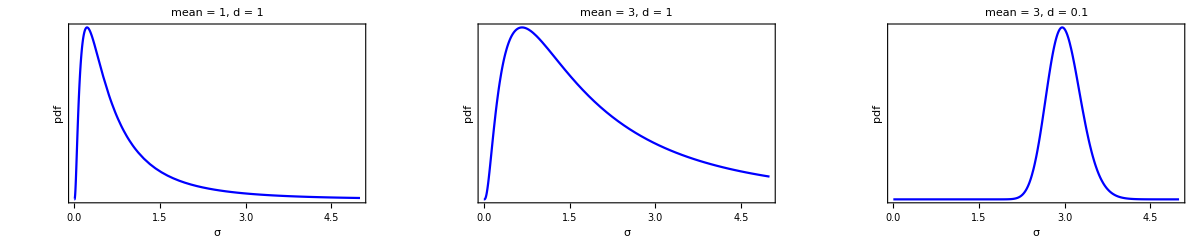

```mathematica
g1=Plot[PDF[aCentredLogNormal[1,1],x],{x,0,5},PlotRange->Full,Evaluate@options3,PlotStyle->Blue,FrameTicks->{True,None},FrameLabel->{"σ","pdf"},PlotLabel->"mean = 1, d = 1"];
g2=Plot[PDF[aCentredLogNormal[3,1],x],{x,0,5},PlotRange->Full,Evaluate@options3,PlotStyle->Blue,FrameTicks->{True,None},FrameLabel->{"σ","pdf"},PlotLabel->"mean = 3, d = 1"];
g3=Plot[PDF[aCentredLogNormal[3,0.1],x],{x,0,5},PlotRange->Full,Evaluate@options3,PlotStyle->Blue,FrameTicks->{True,None},FrameLabel->{"σ","pdf"},PlotLabel->"mean = 3, d = 0.1"];
gFinal=GraphicsRow[{g1,g2,g3},ImageSize->1200]
```

```mathematica
Export["metropolisHastings_asymmetricJumping.pdf",gFinal]
```

metropolisHastings_asymmetricJumping.pdf